x^3+3 x^2-4 x-12

-12

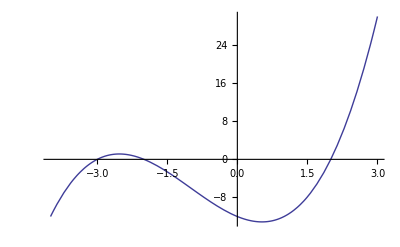

```mathematica
f[x_]:=(x^2-4)(x+3);
f[x]//Expand//TraditionalForm
f[0]
Plot[f[x],{x,-4,3}]
```

```mathematica
3x^2-3x+1+7/(2x^2+1)//Together//ExpandDenominator//TraditionalForm
```

(6 x^4-6 x^3+5 x^2-3 x+8)/(2 x^2+1)

```mathematica
x^2(x+5)-(x+5)//Expand//TraditionalForm
```

x^3+5 x^2-x-5

```mathematica
PolynomialQuotientRemainder[4x^4-4x^3-5x^2+x+8,2x+1,x]//TraditionalForm
```

{2 x^3-3 x^2-x+1,7}

(2 x^2+5 x-3)/(x+2)

{1+2 x,-5}

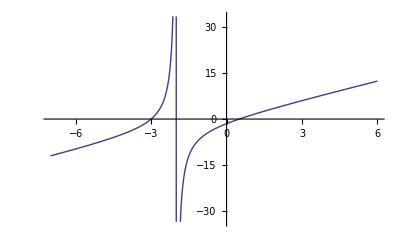

```mathematica
f[x_]:=((2x-1)(x+3))/(x+2);
f[x]//ExpandNumerator//ExpandDenominator//TraditionalForm
PolynomialQuotientRemainder[Numerator[f[x]],Denominator[f[x]],x]
Plot[f[x],{x,-7,6}]
f[0]
```

(x^2+2 x+2)/(x+1)

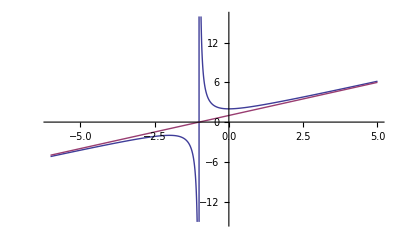

```mathematica
f=x+1+1/(x+1)//Together
Plot[{f,x+1},{x,-6,5}]
```

```mathematica
PolynomialQuotientRemainder[(x+1)(x+2),(x-2),x]
```

{x+5,12}

```mathematica
p=(x-3)(x-(1+2I))(x-(1-2I));
p//Expand//TraditionalForm
```

x^3-5 x^2+11 x-15

```mathematica
(x-(1+2I))(x-(1-2I))//Expand//TraditionalForm
```

x^2-2 x+5

```mathematica
(2-3I)/(3+2I)//ComplexExpand
```

-ⅈ

```mathematica
(2-Sqrt[-9])(Sqrt[-4]+3)//ComplexExpand
```

12-5 ⅈ

```mathematica
(5+I)/(4-2I)//StandardForm
```

9/10+(7 ⅈ)/10

```mathematica
PolynomialQuotientRemainder[3x^3-4x+7,x+2,x]//TraditionalForm
```

{3 x^2-6 x+8,-9}

```mathematica
f[x_]:=x^5+4x^4-15x^3+5x^2+12x-3
f[2]
f[x]//Expand//TraditionalForm
PolynomialQuotientRemainder[f[x],x-2,x]//TraditionalForm
```

17

x^5+4 x^4-15 x^3+5 x^2+12 x-3

{x^4+6 x^3-3 x^2-x+10,17}

```mathematica
(x+3I)(x-3I)(x-2)//Expand//TraditionalForm
```

x^3-2 x^2+9 x-18

```mathematica
(x+3I)(x-3I)(x-2)//Expand
```

x^3-2 x^2+9 x-18

```mathematica
x(x+1)(x+2)+x+1//Expand
```

x^3+3 x^2+3 x+1

```mathematica
PolynomialQuotientRemainder[x^3+3 x^2+3 x+1,x+1,x]
```

{x^2+2 x+1,0}

```mathematica
PolynomialQuotientRemainder[a x +b,c x+d,x]
```

{a/c,b-(a d)/c}

```mathematica
Solve[a/c+b-(a d)/c==(a x+b)/(c x+d),x]
```

{{x→(1-d)/c}}

```mathematica
x
```